```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Dir = "/home/matt/git/source/fast-fourier-transform/fast-fourier/results";
Thread1=Import[StringJoin[Dir,"/1.txt"], "Table"];
Thread2=Import[StringJoin[Dir,"/4.txt"], "Table"];
Thread3=Import[StringJoin[Dir,"/16.txt"], "Table"];
Thread4=Import[StringJoin[Dir,"/64.txt"], "Table"];
Thread5=Import[StringJoin[Dir,"/256.txt"], "Table"];
Thread6=Import[StringJoin[Dir,"/1024.txt"], "Table"];
```

```mathematica
DS1 = Table[{{Thread1[[n]][[1]],Thread1[[n]][[2]]},  ErrorBar[ Thread1[[n]][[3]] ]},{n,1,Length[Thread1]}];
DS2 = Table[{{Thread2[[n]][[1]],Thread2[[n]][[2]]},  ErrorBar[ Thread2[[n]][[3]] ]},{n,1,Length[Thread2]}];
DS3 = Table[{{Thread3[[n]][[1]],Thread3[[n]][[2]]},  ErrorBar[ Thread3[[n]][[3]] ]},{n,1,Length[Thread3]}];
DS4 = Table[{{Thread4[[n]][[1]],Thread4[[n]][[2]]},  ErrorBar[ Thread4[[n]][[3]] ]},{n,1,Length[Thread4]}];
DS5 = Table[{{Thread5[[n]][[1]],Thread5[[n]][[2]]},  ErrorBar[ Thread5[[n]][[3]] ]},{n,1,Length[Thread5]}];
DS6 = Table[{{Thread6[[n]][[1]],Thread6[[n]][[2]]},  ErrorBar[ Thread6[[n]][[3]] ]},{n,1,Length[Thread6]}];
```

```mathematica
DA1 = Table[DS1[[n]][[1]],{n,1,Length[Thread1]}];
DA2 = Table[DS2[[n]][[1]],{n,1,Length[Thread2]}];
DA3 = Table[DS3[[n]][[1]],{n,1,Length[Thread3]}];
DA4 = Table[DS4[[n]][[1]],{n,1,Length[Thread4]}];
DA5 = Table[DS5[[n]][[1]],{n,1,Length[Thread5]}];
DA6 = Table[DS6[[n]][[1]],{n,1,Length[Thread6]}];
```

```mathematica
M1=NonlinearModelFit[DA1,a x^2+b x+c,{a,b,c},x];
M2=NonlinearModelFit[DA2,a x^2+b x+c,{a,b,c},x];
M3=NonlinearModelFit[DA3,a x^2+b x+c,{a,b,c},x];
M4=NonlinearModelFit[DA4,a x^2+b x+c,{a,b,c},x];
M5=NonlinearModelFit[DA5,a x^2+b x+c,{a,b,c},x];
M6=NonlinearModelFit[DA6,a x^2+b x+c,{a,b,c},x];
```

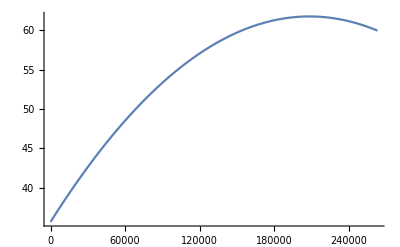

```mathematica
Plot[M1[x],{x,0, 2^(18)+1000}]
```

```mathematica
Err=ErrorListPlot[{DS1,DS2,DS3,DS4,DS5,DS6}];
```

```mathematica
BF = Plot[{M1[x],M2[x],M3[x],M4[x],M5[x],M6[x]},{x,0,2^(18)+1000}, PlotLegends->{"1 Thread","4 Threads" , "16 Threads", "64 Threads", "256 Threads", "1024 Threads"}, PlotRange->{{0,2^(18)+1000},{0,80}}];
```

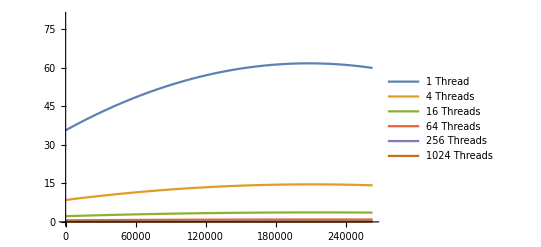

```mathematica
BF
```

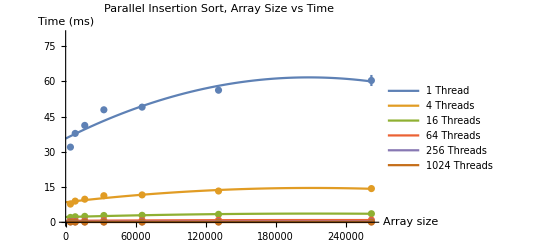

```mathematica
Show[Err,BF,AxesLabel-> {"Array size", "Time (ms)"},PlotRange->{{0,2^(18)+1000},{0,80}}, PlotLabel-> "Parallel Insertion Sort, Array Size vs Time"]
```

```mathematica
Coeffs={{1,M1''[x]/2},{4, M2''[x]/2}, {16,M3''[x]/2}, {64,M4''[x]/2}, {256,M5''[x]/2}, {1024,M6''[x]/2}}
```

{{1,-6.0004×10^-10},{4,-1.36741×10^-10},{16,-3.19424×10^-11},{64,-6.73151×10^-12},{256,-5.99511×10^-13},{1024,9.81246×10^-13}}

```mathematica
Lm=LinearModelFit[Coeffs,x,x]
```

FittedModel[-1.78481×10^-10+2.16713×10^-13 x]

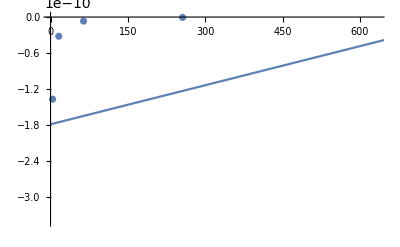

```mathematica
Show[{ListPlot[Coeffs],Plot[Lm[x],{x,1,1024}]}]
```

```mathematica
Coeffs
```

{{1,-6.0004×10^-10},{4,-1.36741×10^-10},{16,-3.19424×10^-11},{64,-6.73151×10^-12},{256,-5.99511×10^-13},{1024,9.81246×10^-13}}

```mathematica
Lm["RSquared"]
```

0.135666